# AOE Thin-Wall Project

Group 7 - Don’t call my name, Don’t call my name, Mariko. That’s not my name, That’s not my name, Manana Got-no-man (Aesthetics), Vyon Coetzer, David Del Grosso, David Gardiner, Gaurav Sakhawala, Ronak Shah

Iteration 3: Stringers at each Corner

```mathematica
ClearAll["Global`*"]
```

ClearAll::wrsym: Symbol σxxLb is Protected.

ClearAll::wrsym: Symbol σxxLc is Protected.

ClearAll::wrsym: Symbol σxxM1b is Protected.

General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.

## Constants

```mathematica
ClearAll["Global`*"]
tf=.018675;
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];

(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.04666 chord[x];*)(*box height (ft)*)
heightL[x_]=.04666*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.04666*chordR[x];
widthR[x_]=.65*chordR[x];
(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.04666*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.04666*chordR[x];*)

JL[x_]=1/3 widthL[x] heightL[x]^3; (*torsion constant 0≤x<27.5*)
JR[x_]=1/3 widthR[x] heightR[x]^3;(*torsion constant 27.5≤x<95.8*)
GCF=104427171.365; (*psf*)

Cm=.016;(*moment coefficient at 11 degree AoA*)

e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=99.88; (*density of CF (lb/ft3)*)
(*tcl[x_]=.001;
tcr[x_]=.005;*)
(*tL[x_]=tf*heightR[95.8]
tR[x_]=tf*heightR[95.8];*)
r = 0.15; (*radius of stringer ft*)
r2 = 0.15;
ASL=π*r^2;
ASR= Pi*r2^2;

tL[x_]=tf*heightR[x];
tR[x_]=tf*heightR[x];

Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])+4*ρAl*ASL,{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])+4*ρAl*ASR,{x,27.5,95.8}];(*weight of spar (lbs)*)

ycL[x_]=heightL[x]/2;
ycR[x_]=heightR[x]/2;
zcL[x_]=widthL[x]/2;
zcR[x_]=widthR[x]/2;
(*IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)*)

AwebL[x_]=tL[x]*(heightL[x]-2*tL[x]);
AwebR[x_]=tR[x]*(heightR[x]-2*tR[x]);


IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2+1/12*tL[x]*(heightL[x]-2*tL[x])^3*2+2*AwebL[x]*((widthL[x]-4tL[x])/6+tL[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]^3*heightL[x]-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2+1/12*(heightL[x]-2*tL[x])*tL[x]^3;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2+1/12*tR[x]*(heightR[x]-2*tR[x])^3*2+2*AwebR[x]*((widthR[x]-4tR[x])/6+tR[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]^3*heightR[x]-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2+1/12*(heightR[x]-2*tR[x])*tR[x]^3;(*moment of inertia of drag (ft4)*)

Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall ;(*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=1461980399.11; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
σy=12531260.6/FS;(*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
Leng = 20;

Cost = Wspar*13.785; (*material cost for spar in $ *)
WC = Wspar/Cost; (*Weight/Cost*)

Wspar
Cost
```

ClearAll::wrsym: Symbol σxxLb is Protected.

ClearAll::wrsym: Symbol σxxLc is Protected.

ClearAll::wrsym: Symbol σxxM1b is Protected.

General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.

8361.72

115266.

## Case 1 (Takeoff)

### Lift

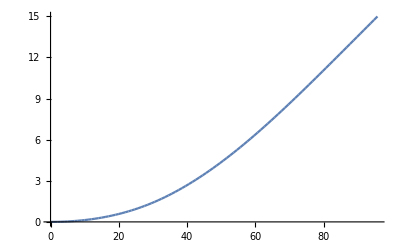

```mathematica
(* distributed load *)
py[x_]=a x^2+b x+c;
Lift  = (1/2 )*ρ*Vto^2*S*clmax*e;
dpy[x_]=D[py[x],x];
eq1a=py[Lw]==0;
eq2a=dpy[0]==0;
eq3a=Integrate[py[x],{x,0,Lw}]==Lift/2;
sol1a=Solve[{eq1a,eq2a,eq3a},{a,b,c}];
a=a/.sol1a[[1]];
b=b/.sol1a[[1]];
c=c/.sol1a[[1]];
py[x_]=py[x];
Integrate[py[x],{x,0,Lw}]; (*total lift*)

PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])+4*ρAl*ASL;
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])+4*ρAl*ASR;

nsLG=10;

Do[
Izzi[i]=1/12 widthL[(i-1)*Llg/nsLG] *heightL[(i-1)*Llg/nsLG]^3-1/12*(widthL[(i-1)*Llg/nsLG]-2tL[(i-1)*Llg/nsLG])*(heightL[(i-1)*Llg/nsLG]-2tL[(i-1)*Llg/nsLG])^3+4*ASL*(ycL[(i-1)*Llg/nsLG])^2+1/12*tL[(i-1)*Llg/nsLG]*(heightL[(i-1)*Llg/nsLG]-2*tL[(i-1)*Llg/nsLG])^3*2+2*AwebL[(i-1)*Llg/nsLG]*((widthL[(i-1)*Llg/nsLG]-4tL[(i-1)*Llg/nsLG])/6+tL[(i-1)*Llg/nsLG]/2)^2;
,{i,1,nsLG}];

Do[
pyi[i][x_]=py[x]-Wfuel/Llg-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,1,nsLG}]

eqi[1]=rotyi[1][0]==0;
eqi[2]=defyi[1][0]==0;
eqi[3]=Vyi[nsLG][Llg]+Wlg==Vyi[nsLG+1][Llg];
eqi[4]=Mzi[nsLG][Llg]==Mzi[nsLG+1][Llg];
nmc=9;

Do[
eqi[4j+1]=Vyi[j][j*Llg/nsLG]==Vyi[j+1][j*Llg/nsLG];
eqi[4j+2]=Mzi[j][j*Llg/nsLG]==Mzi[j+1][j*Llg/nsLG];
eqi[4j+3]=rotyi[j][j*Llg/nsLG]==rotyi[j+1][j*Llg/nsLG];
eqi[4j+4]=defyi[j][j*Llg/nsLG]==defyi[j+1][j*Llg/nsLG];
,{j,1,nmc}];

nsENG=10;
Do[
Izzi[i]=1/12 widthL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG] *heightL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]^3-1/12*(widthL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-2tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])*(heightL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-2tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])^3+4*ASL*(ycL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])^2+1/12*tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]*(heightL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-2*tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])^3*2+2*AwebL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]*(1/6(widthL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-4tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])+tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]/2)^2;
,{i,nsLG+1,nsLG+nsENG}];

Do[
pyi[i][x_]=py[x]-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,1+nsLG,nsLG+nsENG}]

eqi[41]=rotyi[nsLG][Llg]==rotyi[nsLG+1][Llg];
eqi[42]=defyi[nsLG][Llg]==defyi[nsLG+1][Llg];
eqi[43]=Vyi[nsLG+nsENG][Leng]+Weng==Vyi[nsLG+nsENG+1][Leng];
eqi[44]=Mzi[nsLG+nsENG][Leng]==Mzi[nsLG+nsENG+1][Leng];
nmc=9;

Do[
eqi[4j+1]=Vyi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==Vyi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
eqi[4j+2]=Mzi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==Mzi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
eqi[4j+3]=rotyi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==rotyi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
eqi[4j+4]=defyi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==defyi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
,{j,nsLG+1,nmc+nsENG}];

nsTP=8;
Do[
Izzi[i]=1/12 widthL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP] *heightL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]^3-1/12*(widthL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-2tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])*(heightL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-2tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])^3+4*ASL*(ycL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])^2+1/12*tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]*(heightL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-2*tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])^3*2+2*AwebL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]*(1/6(widthL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-4tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])+tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]/2)^2;
,{i,nsLG+nsENG+1,nsLG+nsENG+nsTP}];
Do[
pyi[i][x_]=py[x]-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,1+nsLG+nsENG,nsLG+nsENG+nsTP}]

eqi[81]=rotyi[nsLG+nsENG][Leng]==rotyi[nsLG+nsENG+1][Leng];
eqi[82]=defyi[nsLG+nsENG][Leng]==defyi[nsLG+nsENG+1][Leng];
eqi[83]=Vyi[nsLG+nsENG+nsTP][Ltaper]==Vyi[nsLG+nsENG+nsTP+1][Ltaper];
eqi[84]=Mzi[nsLG+nsENG+nsTP][Ltaper]==Mzi[nsLG+nsENG+nsTP+1][Ltaper];

nmc=7;

Do[
eqi[4j+1]=Vyi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==Vyi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
eqi[4j+2]=Mzi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==Mzi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
eqi[4j+3]=rotyi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==rotyi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
eqi[4j+4]=defyi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==defyi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
,{j,nsLG+nsENG+1,nmc+nsENG+nsLG}];

nsWNG=68;
Do[
Izzi[i]=1/12 widthR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG] *heightR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]^3-1/12*(widthR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-2tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])*(heightR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-2tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])^3+4*ASR*(ycR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])^2+1/12*tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]*(heightR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-2*tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])^3*2+2*AwebR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]*(1/6(widthR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-4tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])+tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]/2)^2;
,{i,nsLG+nsENG+nsTP+1,nsLG+nsENG+nsTP+nsWNG}];

Do[
pyi[i][x_]=py[x]-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,nsLG+nsENG+nsTP+1,nsLG+nsENG+nsTP+nsWNG}];

eqi[113]=rotyi[nsLG+nsENG+nsTP][Ltaper]==rotyi[nsLG+nsENG+nsTP+1][Ltaper];
eqi[114]=defyi[nsLG+nsENG+nsTP][Ltaper]==defyi[nsLG+nsENG+nsTP+1][Ltaper];
eqi[115]=Vyi[nsLG+nsENG+nsTP+nsWNG][Lw]==0;
eqi[116]=Mzi[nsLG+nsENG+nsTP+nsWNG][Lw]==0;

nmc=67;
Do[
eqi[4j+1]=Vyi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==Vyi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
eqi[4j+2]=Mzi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==Mzi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
eqi[4j+3]=rotyi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==rotyi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
eqi[4j+4]=defyi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==defyi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
,{j,nsLG+nsENG+nsTP+1,nmc+nsENG+nsLG+nsTP}];



soll=Solve[Table[eqi[n],{n,384}],Table[ci[n],{n,384}]];

Do[
ci[i]=ci[i]/.soll[[1]];
,{i,1,384}];

Do[
pltdefi[i]=Plot[defyi[i][x],{x,(i-1)*Llg/nsLG,i*Llg/nsLG}];
,{i,1,nsLG}];
Do[
pltdefi[i]=Plot[defyi[i][x],{x,Llg+(i-1-nsLG)*(Leng-Llg)/nsENG,Llg+(i-nsLG)*(Leng-Llg)/nsENG}];
,{i,nsLG+1,nsLG+nsENG}];
Do[
pltdefi[i]=Plot[defyi[i][x],{x,Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP,Leng+(i-nsLG-nsENG)*(Ltaper-Leng)/nsTP}];
,{i,nsLG+nsENG+1,nsLG+nsENG+nsTP}];
Do[
pltdefi[i]=Plot[defyi[i][x],{x,Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG,Ltaper+(i-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG}];
,{i,nsLG+nsENG+nsTP+1,nsLG+nsENG+nsTP+nsWNG}];

Show[Table[pltdefi[n],{n,nsLG+nsENG+nsTP+nsWNG}],PlotRange->{{0,Lw},{0,defyi[96][Lw]}}]
```

14.9903

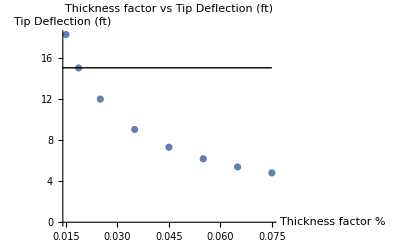

```mathematica
defyi[96][Lw]

vec={{.075,4.79357},{.065,5.37636},{.055,6.164951},{.045,7.287565},{.035,9.007493},{.025,11.96493},{.015,18.2322},{.018675,14.99}};

lplot1 = ListPlot[vec,PlotLabel->"Thickness factor vs Tip Deflection (ft)",AxesLabel->{"Thickness factor %","Tip Deflection (ft)"}];
ln1=Graphics@Line[{{0,15},{.075,15}}];
Show[{lplot1,ln1}]
```

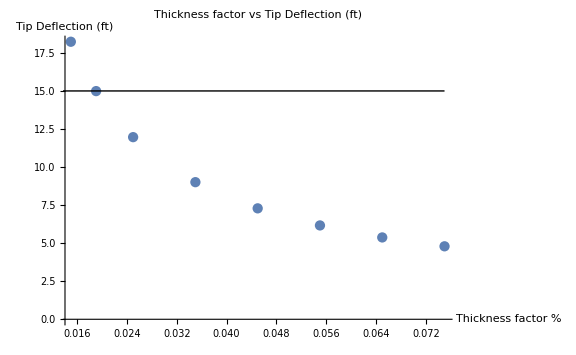

```mathematica
Show[%24989,ImageSize->Large]
```

### Torsion

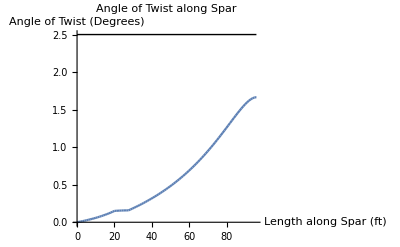

```mathematica
MtL[x_]=1/2 ρ Vto^2 S chordL[x]Cm;
MtR[x_]=1/2 ρ Vto^2 S chordR[x]Cm;

(*0<x<Leng*)
nsENGj=20;
Do[
Ji[i]=1/3 widthL[(i)Leng/nsENGj] heightL[(i)Leng/nsENGj]^3;
,{i,1,nsENGj}]; 
Do[
Mti[i][x_]=MtL[x]+cij[2i-1];
ϕti[i][x_]=Integrate[(Mti[i][x])/(GCF*Ji[i]),x]+cij[2i];
,{i,1,nsENGj}];

eqij[1]=ϕti[1][0]==0;
eqij[2]=Mti[nsENGj][Leng]+Leng*18.5-T*3==Mti[nsENGj+1][Leng];
nmc=19;
Do[
eqij[2j+1]=Mti[j][j Leng/nsENGj]==Mti[j+1][j Leng/nsENGj];
eqij[2j+2]=ϕti[j][j Leng/nsENGj]==ϕti[j+1][j Leng/nsENGj];
,{j,1,nmc}];

(*Leng < x < Ltaper*)
nsTPj=8;
Do[
Ji[i]=1/3 widthL[Leng+(i-nsENGj)*(Ltaper-Leng)/nsTPj] heightL[Leng+(i-nsENGj)*(Ltaper-Leng)/nsTPj]^3;
,{i,1+nsENGj,nsENGj+nsTPj}]; 
Do[
Mti[i][x_]=MtL[x]+cij[2i-1];
ϕti[i][x_]=Integrate[(Mti[i][x])/(GCF*Ji[i]),x]+cij[2i];
,{i,1+nsENGj,nsENGj+nsTPj}];
eqij[41]=ϕti[nsENGj][Leng]==ϕti[nsENGj+1][Leng];
eqij[42]=Mti[nsENGj+nsTPj][Ltaper]==ϕti[nsENGj+nsTPj+1][Ltaper];
nmc=7;
Do[
eqij[2j+1]=Mti[j][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj]==Mti[j+1][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj];
eqij[2j+2]=ϕti[j][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj]==ϕti[j+1][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj];
,{j,1+nsENGj,nsENGj+nmc}];

(*Ltaper<x<Lw*)
nsLWj=68;
Do[
Ji[i]=1/3 widthR[Ltaper+(i-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj] heightR[Ltaper+(i-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]^3;
,{i,1+nsENGj+nsTPj,nsENGj+nsTPj+nsLWj}]; 
Do[
Mti[i][x_]=MtR[x]+cij[2i-1];
ϕti[i][x_]=Integrate[(Mti[i][x])/(GCF*Ji[i]),x]+cij[2i];
,{i,1+nsENGj+nsTPj,nsENGj+nsTPj+nsLWj}];
eqij[57]=ϕti[nsENGj+nsTPj][Ltaper]==ϕti[nsENGj+nsTPj+1][Ltaper];
eqij[58]=Mti[nsENGj+nsTPj+nsLWj][Lw]==0;
nmc=67;
Do[
eqij[2j+1]=Mti[j][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]==Mti[j+1][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj];
eqij[2j+2]=ϕti[j][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]==ϕti[j+1][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj];
,{j,1+nsENGj+nsTPj,nsENGj+nsTPj+nmc}];
solj=Solve[Table[eqij[n],{n,192}],Table[cij[n],{n,192}]];

Do[
cij[i]=cij[i]/.solj[[1]];
,{i,1,192}];

Do[
plttwist[i]=Plot[ϕti[i][x]*180/π,{x,(i-1)*Leng/nsENGj,i*Leng/nsENGj}];
,{i,1,nsENGj}];
Do[
plttwist[i]=Plot[ϕti[i][x]*180/π,{x,Leng+(i-1-nsENGj)*(Ltaper-Leng)/nsTPj,Leng+(i-nsENGj)*(Ltaper-Leng)/nsTPj}];
,{i,nsENGj+1,nsENGj+nsTPj}];
Do[
plttwist[i]=Plot[ϕti[i][x]*180/π,{x,Ltaper+(i-1-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj,Ltaper+(i-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj}];
,{i,nsENGj+nsTPj+1,nsENGj+nsTPj+nsLWj}];


Do[
maxdi[i]=√((heightL[(i-.5)*Leng/nsENGj]/2)^2+(widthL[(i-.5)*Leng/nsENGj]/2)^2);
,{i,1,nsENGj}];
Do[
maxdi[i]=√((heightL[Leng+(i-.5-nsENGj)*(Ltaper-Leng)/nsTPj]/2)^2+(widthL[Leng+(i-.5-nsENGj)*(Ltaper-Leng)/nsTPj]/2)^2);
,{i,1+nsENGj,nsENGj+nsTPj}];
Do[
maxdi[i]=√((heightR[Ltaper+(i-.5-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]/2)^2+(widthR[Ltaper+(i-.5-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]/2)^2);
,{i,1+nsENGj+nsTPj,nsENGj+nsTPj+nsLWj}];

Do[
σxθi[i][x_]=(Mti[i][x]*maxdi[i])/Ji[i];
,{i,1,96}];







ln3=Graphics@Line[{{0,2.5},{Lw,2.5}}];

Show[{Table[plttwist[n],{n,nsENGj+nsTPj+nsLWj}],ln3},PlotRange->{{0,Lw},{0,2.5}},PlotLabel->"Angle of Twist along Spar",PlotLabel->{"Lenght along Spar (ft)","Angle of Twist^O"},AxesLabel->{"Length along Spar (ft)","Angle of Twist (Degrees)"}]
```

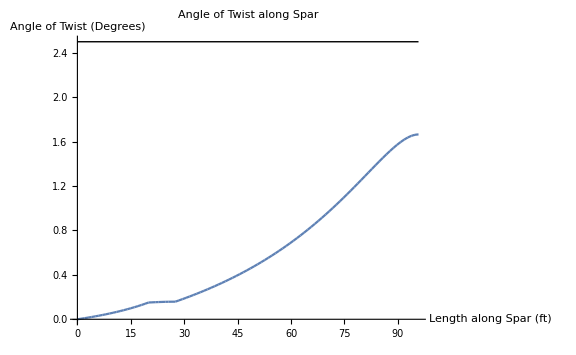

```mathematica
Show[%36946,ImageSize->Large]
```

### Drag

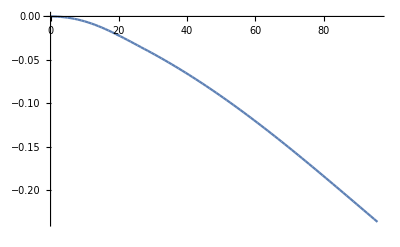

```mathematica
pzL[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);
pzM[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);
pzR[x_]=-(1/2 ρ Vto^2 S cd)/Lw-py[x]^2/((1/2 ρ Vto^2 S π *e*AR)/Lw);


nsENGd=20;

Do[
Iyyi[i]=1/12 widthL[(i-1)Leng/nsENGd]^3*heightL[(i-1)Leng/nsENGd]-1/12*(heightL[(i-1)Leng/nsENGd]-2tL[(i-1)Leng/nsENGd])*(widthL[(i-1)Leng/nsENGd]-2tL[(i-1)Leng/nsENGd])^3+4*ASL*(zcL[(i-1)Leng/nsENGd])^2+1/12*(heightL[(i-1)Leng/nsENGd]-2*tL[(i-1)Leng/nsENGd])*tL[(i-1)Leng/nsENGd]^3;
,{i,1,nsENGd}];

Do[
pzi[i][x_]=pzL[x];
Vzi[i][x_]=Integrate[-pzi[i][x],x]+cid[4i-3];
Myi[i][x_]=Integrate[Vzi[i][x],x]+cid[4i-2];
rotzi[i][x_]=Integrate[(-Myi[i][x])/(EE*Iyyi[i]),x]+cid[4i-1];
defzi[i][x_]=Integrate[rotzi[i][x],x]+cid[4i];
,{i,1,nsENGd}];
eqid[1]=rotzi[1][0]==0;
eqid[2]=defzi[1][0]==0;
eqid[3]=Vzi[nsENGd][Leng]+T==Vzi[nsENGd+1][Leng];
eqid[4]=Myi[nsENGd][Leng]==Myi[nsENGd+1][Leng];

nmc=19;
Do[
eqid[4j+1]=Vzi[j][j*Leng/nsENGd]==Vzi[j+1][j*Leng/nsENGd];
eqid[4j+2]=Myi[j][j*Leng/nsENGd]==Myi[j+1][j*Llg/nsENGd];
eqid[4j+3]=rotzi[j][j*Leng/nsENGd]==rotzi[j+1][j*Leng/nsENGd];
eqid[4j+4]=defzi[j][j*Leng/nsENGd]==defzi[j+1][j*Leng/nsENGd];
,{j,1,nmc}];

nsTPd=8;
Do[
Iyyi[i]=1/12 widthL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]^3*heightL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]-1/12*(heightL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]-2tL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd])*(widthL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]-2tL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd])^3+4*ASL*(zcL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd])^2+1/12*(heightL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]-2*tL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd])*tL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]^3;
,{i,1+nsENGd,nsENGd+nsTPd}];
Do[
pzi[i][x_]=pzL[x];
Vzi[i][x_]=Integrate[-pzi[i][x],x]+cid[4i-3];
Myi[i][x_]=Integrate[Vzi[i][x],x]+cid[4i-2];
rotzi[i][x_]=Integrate[(-Myi[i][x])/(EE*Iyyi[i]),x]+cid[4i-1];
defzi[i][x_]=Integrate[rotzi[i][x],x]+cid[4i];
,{i,1+nsENGd,nsENGd+nsTPd}];
eqid[81]=rotzi[nsENGd][Leng]==rotzi[nsENGd+1][Leng];
eqid[82]=defzi[nsENGd][Leng]==defzi[nsENGd+1][Leng];
eqid[83]=Vzi[nsENGd+nsTPd][Ltaper]==Vzi[nsENGd+nsTPd+1][Ltaper];
eqid[84]=Myi[nsENGd+nsTPd][Ltaper]==Myi[nsENGd+nsTPd+1][Ltaper];
nmc=7;
Do[
eqid[4j+1]=Vzi[j][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd]==Vzi[j+1][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd];
eqid[4j+2]=Myi[j][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd]==Myi[j+1][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd];
eqid[4j+3]=rotzi[j][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd]==rotzi[j+1][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd];
eqid[4j+4]=defzi[j][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd]==defzi[j+1][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd];
,{j,1+nsENGd,nsENGd+nmc}];

nsLWd=68;
Do[
Iyyi[i]=1/12 widthR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]^3*heightR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]-1/12*(heightR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]-2tR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd])*(widthR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]-2tR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd])^3+4*ASR*(zcR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd])^2+1/12*(heightR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]-2*tR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd])*tR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]^3;
,{i,1+nsENGd+nsTPd,nsENGd+nsTPd+nsLWd}];
Do[
pzi[i][x_]=pzL[x];
Vzi[i][x_]=Integrate[-pzi[i][x],x]+cid[4i-3];
Myi[i][x_]=Integrate[Vzi[i][x],x]+cid[4i-2];
rotzi[i][x_]=Integrate[(-Myi[i][x])/(EE*Iyyi[i]),x]+cid[4i-1];
defzi[i][x_]=Integrate[rotzi[i][x],x]+cid[4i];
,{i,1+nsENGd+nsTPd,nsENGd+nsTPd+nsLWd}];
eqid[113]=rotzi[nsENGd+nsTPd][Ltaper]==rotzi[nsENGd+nsTPd+1][Ltaper];
eqid[114]=defzi[nsENGd+nsTPd][Ltaper]==defzi[nsENGd+nsTPd+1][Ltaper];
eqid[115]=Vzi[nsENGd+nsTPd+nsLWd][Lw]==0;
eqid[116]=Myi[nsENGd+nsTPd+nsLWd][Lw]==0;
nmc=67;
Do[
eqid[4j+1]=Vzi[j][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]==Vzi[j+1][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd];
eqid[4j+2]=Myi[j][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]==Myi[j+1][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd];
eqid[4j+3]=rotzi[j][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]==rotzi[j+1][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd];
eqid[4j+4]=defzi[j][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]==defzi[j+1][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd];
,{j,1+nsENGd+nsTPd,nsENGd+nsTPd+nmc}];

sold=Solve[Table[eqid[n],{n,384}],Table[cid[n],{n,384}]];

Do[
cid[i]=cid[i]/.sold[[1]];
,{i,1,384}];

Do[
pltdefid[i]=Plot[defzi[i][x],{x,(i-1)*Leng/nsENGd,i*Leng/nsENGd}];
,{i,1,nsENGd}];
Do[
pltdefid[i]=Plot[defzi[i][x],{x,Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd,Leng+(i-nsLG)*(Ltaper-Leng)/nsTPd}];
,{i,nsENGd+1,nsENGd+nsTPd}];
Do[
pltdefid[i]=Plot[defzi[i][x],{x,Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd,Ltaper+(i-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd}];
,{i,nsLG+nsENG+1,nsENGd+nsTPd+nsLWd}];


Show[Table[pltdefid[n],{n,nsENGd+nsTPd+nsLWd}],PlotRange->{{0,Lw},{0,defzi[96][Lw]}}]
```

### Stress

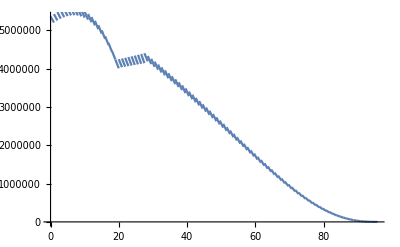

Show::gcomb: Could not combine the graphics objects in ….

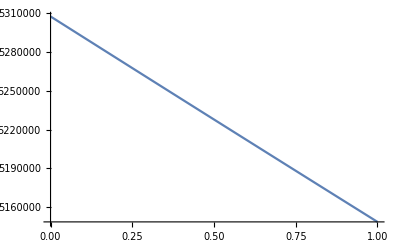
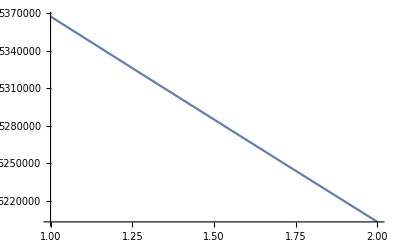
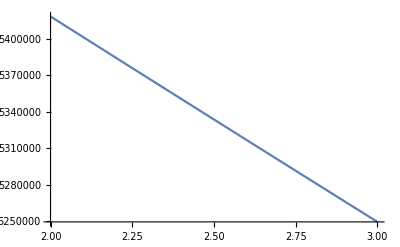
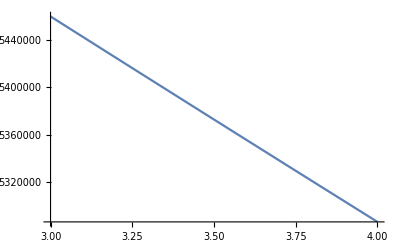
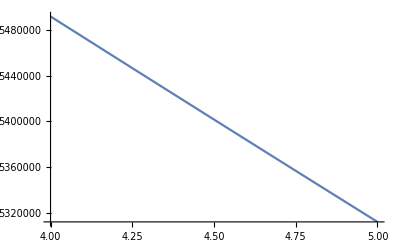
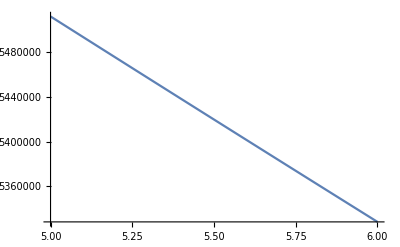
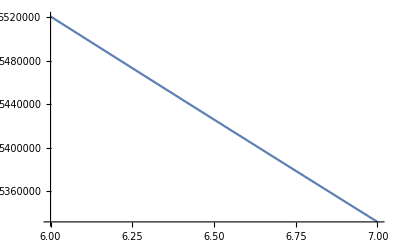
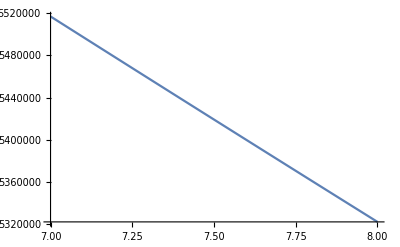
Show[{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-},PlotRange→{{0,95.8},{0,1.08967×10^7}},AxesOrigin→{0,0},Null]

```mathematica
nsLGσ=10;
nsENGσ=10;
nsTPσ=8;
nsLWσ=68;

Do[
σxxi[i][x_]=Abs[(Myi[i][x]*(-widthL[x])/2)/Iyyi[i]]+Abs[(Mzi[i][x]*heightL[x]/2)/Izzi[i]];
,{i,1,28}];
nsENGσ=10;
Do[
σxxi[i][x_]=Abs[(Myi[i][x]*(-widthR[x])/2)/Iyyi[i]]+Abs[(Mzi[i][x]*heightR[x]/2)/Izzi[i]];
,{i,1+28,96}];

Do[
pltσi[i]=Plot[σxxi[i][x],{x,(i-1)*Llg/nsLGσ,i*Llg/nsLGσ}];
,{i,1,nsLGσ}];
Do[
pltσi[i]=Plot[σxxi[i][x],{x,Llg+(i-1-nsLGσ)*(Leng-Llg)/nsENGσ,Llg+(i-nsLGσ)*(Leng-Llg)/nsENGσ}];
,{i,nsLGσ+1,nsLGσ+nsENGσ}];
Do[
pltσi[i]=Plot[σxxi[i][x],{x,Leng+(i-1-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ,Leng+(i-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ}];
,{i,nsLGσ+nsENGσ+1,nsLGσ+nsENGσ+nsTPσ}];
Do[
pltσi[i]=Plot[σxxi[i][x],{x,Ltaper+(i-1-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ,Ltaper+(i-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ}];
,{i,nsLGσ+nsENGσ+nsTPσ+1,nsLGσ+nsENGσ+nsTPσ+nsLWσ}];

(*Von Mises*)
θ=ArcTan[heightL[0]/widthL[0]];
Do[
σyyi[i][x_]=σxθi[i][x]*Sin[θ];
σzzi[i][x_]=σxθi[i][x]*Cos[θ];
,{i,1,96}];

Do[
σxyi[i][x_]=0;
σxzi[i][x_]=0;
,{i,1,96}];

Do[
σMisesi[i][x_]=√(1/2((σxxi[i][x]-σyyi[i][x])^2+(σyyi[i][x]-σzzi[i][x])^2+(σzzi[i][x]-σxxi[i][x])^2+6((σxyi[i][x])^2+(σxzi[i][x])^2)));
,{i,1,96}]

Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,(i-1)*Llg/nsLGσ,i*Llg/nsLGσ}];
,{i,1,nsLGσ}];
Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,Llg+(i-1-nsLGσ)*(Leng-Llg)/nsENGσ,Llg+(i-nsLGσ)*(Leng-Llg)/nsENGσ}];
,{i,nsLGσ+1,nsLGσ+nsENGσ}];
Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,Leng+(i-1-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ,Leng+(i-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ}];
,{i,nsLGσ+nsENGσ+1,nsLGσ+nsENGσ+nsTPσ}];
Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,Ltaper+(i-1-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ,Ltaper+(i-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ}];
,{i,nsLGσ+nsENGσ+nsTPσ+1,nsLGσ+nsENGσ+nsTPσ+nsLWσ}];







Show[Table[pltσi[n],{n,nsLGσ+nsENGσ+nsTPσ+nsLWσ}],PlotRange->{{0,Lw},{0,σxxi[1][0]}},AxesOrigin->{0,0}]

ln2=Graphics@Line[{{0,σy},{Lw,σy}}];

Show[{Table[pltσMi[n],{n,nsLGσ+nsENGσ+nsTPσ+nsLWσ}],ln2},PlotRange->{{0,Lw},{0,σy}},AxesOrigin->{0,0},]
```

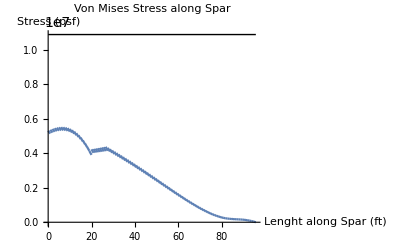

```mathematica
Show[%35291,AxesLabel->{HoldForm["Lenght along Spar (ft)"],HoldForm["Stress (psf)"]},PlotLabel->HoldForm[Von Mises Stress along Spar],LabelStyle->{GrayLevel[0]}]
```

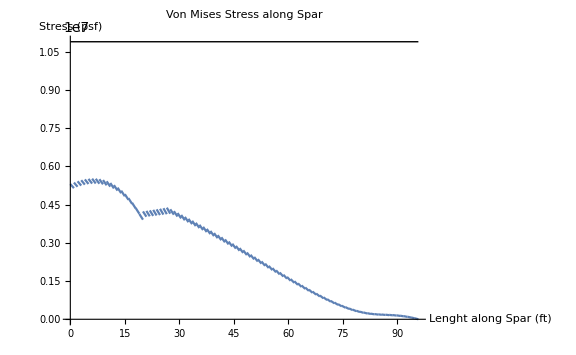

```mathematica
Show[%37005,ImageSize->Large]
```

```mathematica
σy
σMisesi[5][4]


vec={{.075,1.69362},{.065,1.91967},{.055,2.22222},{.045,2.64767},{.035,3.28987},{.025,4.37322},{.015,6.61212},{.01906,5.49154}}
```

1.08967×10^7

5.49154×10^6

{{0.075,1.69362},{0.065,1.91967},{0.055,2.22222},{0.045,2.64767},{0.035,3.28987},{0.025,4.37322},{0.015,6.61212},{0.01906,5.49154}}

### Deflection

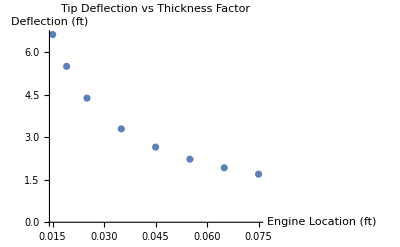

```mathematica
ListPlot[{vec},PlotLabel->"Tip Deflection vs Thickness Factor",AxesLabel->{"Engine Location (ft)","Deflection (ft)"}]
```

### Overall Plots

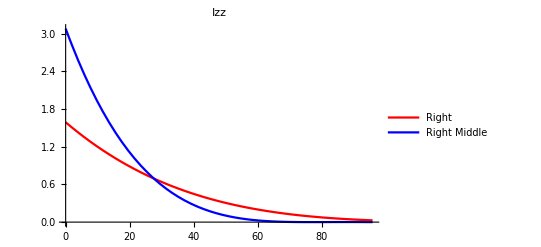

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
pl1=Plot[IzzR[x],{x,0,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
pl2=Plot[IzzL[x],{x,0,Lw},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
Show[{pl1,pl2},PlotRange->All,PlotLabel->"Izz",AxesOrigin->{0,0}]

pl3=Plot[VyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl4=Plot[VyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl5=Plot[VyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl6=Plot[VyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl3,pl4,pl5,pl6},PlotRange->All,PlotLabel->"Vy",AxesOrigin->{0,0}]

pl7=Plot[MzL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl8=Plot[MzLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl9=Plot[MzRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl10=Plot[MzR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl7,pl8,pl9,pl10},PlotRange->All,PlotLabel->"Mz",AxesOrigin->{0,0}]

pl11=Plot[rotyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl12=Plot[rotyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl13=Plot[rotyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl14=Plot[rotyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl11,pl12,pl13,pl14},PlotRange->All,PlotLabel->"roty",AxesOrigin->{0,0}]

pl15=Plot[uyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl16=Plot[uyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl17=Plot[uyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl18=Plot[uyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl15,pl16,pl17,pl18},PlotRange->All,PlotLabel->"uy",AxesOrigin->{0,0}]
```

### Comments

```mathematica
(*tf={height/4,height/8,height/20,height/50,height/100};
Leng=20;
dataL=Transpose@{t,σxxR[27.5]};
(*Leng=(52.3+20)/2;
dataM=Transpose@{tf,σxx};
Leng=52.3;
dataR=Transpose@{t,σxx};
ListPlot[{dataL,dataM,dataR},PlotLegends->{"Leftmost Engine","Central Engine","Rightmost Engine"}]*)
ListPlot[{dataL}]*)

(*thick={height/4,height/8,height/12,height/15,height/20,height/25,height/50,height/100};
data1=Transpose@{thick,tipdeflection[Lw,20,thick]};
data2=Transpose@{thick,tipdeflection[Lw,(52.3+20)/2,thick]};
data3=Transpose@{thick,tipdeflection[Lw,52.3,thick]}*)
```

## Constants

```mathematica
ClearAll["Global`*"]
tf=.018675;
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];

AwebL[x_]=tL[x]*(heightL[x]-2*tL[x]);
AwebR[x_]=tR[x]*(heightR[x]-2*tR[x]);

(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.04666 chord[x];*)(*box height (ft)*)
heightL[x_]=.04666*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.04666*chordR[x];
widthR[x_]=.65*chordR[x];
(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.04666*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.04666*chordR[x];*)

JL[x_]=1/3 widthL[x] heightL[x]^3; (*torsion constant 0≤x<27.5*)
JR[x_]=1/3 widthR[x] heightR[x]^3;(*torsion constant 27.5≤x<95.8*)
GCF=104427171.365; (*psf*)

Cm=.016;(*moment coefficient at 11 degree AoA*)


e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10.06; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=3.1; (*density of aluminum (lb/ft3)*)
(*tcl[x_]=.001;
tcr[x_]=.005;*)
(*tL[x_]=tf*heightR[95.8]
tR[x_]=tf*heightR[95.8];*)
r = 0.15; (*radius of stringer ft*)
r2 = 0.15;
ASL=π*r^2;
ASR= Pi*r2^2;

tL[x_]=tf*heightR[x];
tR[x_]=tf*heightR[x];

Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])+4*ρAl*ASL,{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])+4*ρAl*ASR,{x,27.5,95.8}];(*weight of spar (lbs)*)

ycL[x_]=heightL[x]/2;
ycR[x_]=heightR[x]/2;
zcL[x_]=widthL[x]/2;
zcR[x_]=widthR[x]/2;
(*IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)*)

IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2+1/12*tL[x]*(heightL[x]-2*tL[x])^3*2+2*AwebL[x]*((widthL[x]-4tL[x])/6+tL[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2+1/12*(heightL[x]-2*tL[x])*tL[x]^3;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2+1/12*tR[x]*(heightR[x]-2*tR[x])^3*2+2*AwebR[x]*((widthR[x]-4tR[x])/6+tR[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2+1/12*(heightR[x]-2*tR[x])*tR[x]^3;(*moment of inertia of drag (ft4)*)
Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=1461980399.11; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS;(*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
Leng = 20;

Cost = Wspar*10; (*material cost for spar in $ *)
WC = Wspar/Cost; (*Weight/Cost*)
```

ClearAll::wrsym: Symbol σxxLb is Protected.

ClearAll::wrsym: Symbol σxxLc is Protected.

ClearAll::wrsym: Symbol σxxM1b is Protected.

General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.

## Case 2 (Engine Failure)

### Lift

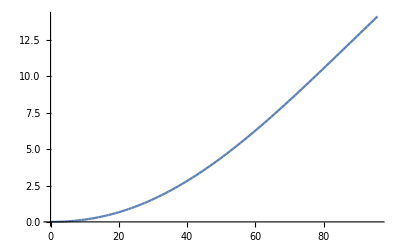

```mathematica
(* distributed load *)
py[x_]=a x^2+b x+c;
(*Lift  = (1/2 )*ρ35k*Vcruise^2*S*clmax*e;*)
dpy[x_]=D[py[x],x];
eq1a=py[Lw]==0;
eq2a=dpy[0]==0;
eq3a=Integrate[py[x],{x,0,Lw}]==Wto/2;
sol1a=Solve[{eq1a,eq2a,eq3a},{a,b,c}];
a=a/.sol1a[[1]];
b=b/.sol1a[[1]];
c=c/.sol1a[[1]]; 
py[x_]=py[x];
Integrate[py[x],{x,0,Lw}]; (*total lift*)

PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x]);
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x]);

nsLG=10;

Do[
Izzi[i]=1/12 widthL[(i-1)*Llg/nsLG] *heightL[(i-1)*Llg/nsLG]^3-1/12*(widthL[(i-1)*Llg/nsLG]-2tL[(i-1)*Llg/nsLG])*(heightL[(i-1)*Llg/nsLG]-2tL[(i-1)*Llg/nsLG])^3+4*ASL*(ycL[(i-1)*Llg/nsLG])^2+1/12*tL[(i-1)*Llg/nsLG]*(heightL[(i-1)*Llg/nsLG]-2*tL[(i-1)*Llg/nsLG])^3*2+2*AwebL[(i-1)*Llg/nsLG]*((widthL[(i-1)*Llg/nsLG]-4tL[(i-1)*Llg/nsLG])/6+tL[(i-1)*Llg/nsLG]/2)^2;
,{i,1,nsLG}];

Do[
pyi[i][x_]=py[x]-Wfuel/Llg-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,1,nsLG}]

eqi[1]=rotyi[1][0]==0;
eqi[2]=defyi[1][0]==0;
eqi[3]=Vyi[nsLG][Llg]+Wlg==Vyi[nsLG+1][Llg];
eqi[4]=Mzi[nsLG][Llg]==Mzi[nsLG+1][Llg];
nmc=9;

Do[
eqi[4j+1]=Vyi[j][j*Llg/nsLG]==Vyi[j+1][j*Llg/nsLG];
eqi[4j+2]=Mzi[j][j*Llg/nsLG]==Mzi[j+1][j*Llg/nsLG];
eqi[4j+3]=rotyi[j][j*Llg/nsLG]==rotyi[j+1][j*Llg/nsLG];
eqi[4j+4]=defyi[j][j*Llg/nsLG]==defyi[j+1][j*Llg/nsLG];
,{j,1,nmc}];

nsENG=10;
Do[
Izzi[i]=1/12 widthL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG] *heightL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]^3-1/12*(widthL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-2tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])*(heightL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-2tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])^3+4*ASL*(ycL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])^2+1/12*tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]*(heightL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-2*tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])^3*2+2*AwebL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]*(1/6(widthL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-4tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])+tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]/2)^2;
,{i,nsLG+1,nsLG+nsENG}];

Do[
pyi[i][x_]=py[x]-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,1+nsLG,nsLG+nsENG}]

eqi[41]=rotyi[nsLG][Llg]==rotyi[nsLG+1][Llg];
eqi[42]=defyi[nsLG][Llg]==defyi[nsLG+1][Llg];
eqi[43]=Vyi[nsLG+nsENG][Leng]+Weng==Vyi[nsLG+nsENG+1][Leng];
eqi[44]=Mzi[nsLG+nsENG][Leng]==Mzi[nsLG+nsENG+1][Leng];
nmc=9;

Do[
eqi[4j+1]=Vyi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==Vyi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
eqi[4j+2]=Mzi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==Mzi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
eqi[4j+3]=rotyi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==rotyi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
eqi[4j+4]=defyi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==defyi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
,{j,nsLG+1,nmc+nsENG}];

nsTP=8;
Do[
Izzi[i]=1/12 widthL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP] *heightL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]^3-1/12*(widthL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-2tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])*(heightL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-2tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])^3+4*ASL*(ycL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])^2+1/12*tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]*(heightL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-2*tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])^3*2+2*AwebL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]*(1/6(widthL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-4tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])+tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]/2)^2;
,{i,nsLG+nsENG+1,nsLG+nsENG+nsTP}];
Do[
pyi[i][x_]=py[x]-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,1+nsLG+nsENG,nsLG+nsENG+nsTP}]

eqi[81]=rotyi[nsLG+nsENG][Leng]==rotyi[nsLG+nsENG+1][Leng];
eqi[82]=defyi[nsLG+nsENG][Leng]==defyi[nsLG+nsENG+1][Leng];
eqi[83]=Vyi[nsLG+nsENG+nsTP][Lw]==Vyi[nsLG+nsENG+nsTP+1][Ltaper];
eqi[84]=Mzi[nsLG+nsENG+nsTP][Ltaper]==Mzi[nsLG+nsENG+nsTP+1][Ltaper];

nmc=7;

Do[
eqi[4j+1]=Vyi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==Vyi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
eqi[4j+2]=Mzi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==Mzi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
eqi[4j+3]=rotyi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==rotyi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
eqi[4j+4]=defyi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==defyi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
,{j,nsLG+nsENG+1,nmc+nsENG+nsLG}];

nsWNG=68;
Do[
Izzi[i]=1/12 widthR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG] *heightR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]^3-1/12*(widthR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-2tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])*(heightR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-2tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])^3+4*ASR*(ycR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])^2+1/12*tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]*(heightR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-2*tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])^3*2+2*AwebR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]*(1/6(widthR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-4tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])+tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]/2)^2;
,{i,nsLG+nsENG+nsTP+1,nsLG+nsENG+nsTP+nsWNG}];

Do[
pyi[i][x_]=py[x]-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,nsLG+nsENG+nsTP+1,nsLG+nsENG+nsTP+nsWNG}];

eqi[113]=rotyi[nsLG+nsENG+nsTP][Ltaper]==rotyi[nsLG+nsENG+nsTP+1][Ltaper];
eqi[114]=defyi[nsLG+nsENG+nsTP][Ltaper]==defyi[nsLG+nsENG+nsTP+1][Ltaper];
eqi[115]=Vyi[nsLG+nsENG+nsTP+nsWNG][Lw]==0;
eqi[116]=Mzi[nsLG+nsENG+nsTP+nsWNG][Lw]==0;

nmc=67;
Do[
eqi[4j+1]=Vyi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==Vyi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
eqi[4j+2]=Mzi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==Mzi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
eqi[4j+3]=rotyi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==rotyi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
eqi[4j+4]=defyi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==defyi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
,{j,nsLG+nsENG+nsTP+1,nmc+nsENG+nsLG+nsTP}];



soll=Solve[Table[eqi[n],{n,384}],Table[ci[n],{n,384}]];

Do[
ci[i]=ci[i]/.soll[[1]];
,{i,1,384}];

Do[
pltdefi[i]=Plot[defyi[i][x],{x,(i-1)*Llg/nsLG,i*Llg/nsLG}];
,{i,1,nsLG}];
Do[
pltdefi[i]=Plot[defyi[i][x],{x,Llg+(i-1-nsLG)*(Leng-Llg)/nsENG,Llg+(i-nsLG)*(Leng-Llg)/nsENG}];
,{i,nsLG+1,nsLG+nsENG}];
Do[
pltdefi[i]=Plot[defyi[i][x],{x,Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP,Leng+(i-nsLG-nsENG)*(Ltaper-Leng)/nsTP}];
,{i,nsLG+nsENG+1,nsLG+nsENG+nsTP}];
Do[
pltdefi[i]=Plot[defyi[i][x],{x,Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG,Ltaper+(i-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG}];
,{i,nsLG+nsENG+nsTP+1,nsLG+nsENG+nsTP+nsWNG}];

Show[Table[pltdefi[n],{n,nsLG+nsENG+nsTP+nsWNG}],PlotRange->{{0,Lw},{0,defyi[96][Lw]}}]
```

```mathematica
defyi[96][Lw]
```

14.1133

### Torsion

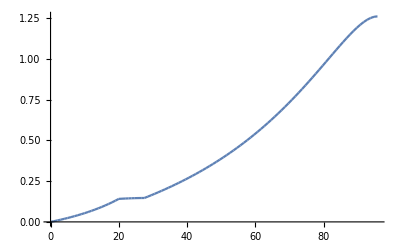

```mathematica
MtL[x_]=1/2 ρ35k Vcruise^2 S chordL[x]Cm;
MtM[x_]=1/2 ρ35k Vcruise^2 S chordL[x]Cm;
MtR[x_]=1/2 ρ35k Vcruise^2 S chordR[x]Cm;

(*0<x<Leng*)
nsENGj=20;
Do[
Ji[i]=1/3 widthL[(i)Leng/nsENGj] heightL[(i)Leng/nsENGj]^3;
,{i,1,nsENGj}]; 
Do[
Mti[i][x_]=MtL[x]+cij[2i-1];
ϕti[i][x_]=Integrate[(Mti[i][x])/(GCF*Ji[i]),x]+cij[2i];
,{i,1,nsENGj}];

eqij[1]=ϕti[1][0]==0;
eqij[2]=Mti[nsENGj][Leng]+Leng*18.5-T*3==Mti[nsENGj+1][Leng];
nmc=19;
Do[
eqij[2j+1]=Mti[j][j Leng/nsENGj]==Mti[j+1][j Leng/nsENGj];
eqij[2j+2]=ϕti[j][j Leng/nsENGj]==ϕti[j+1][j Leng/nsENGj];
,{j,1,nmc}];

(*Leng < x < Ltaper*)
nsTPj=8;
Do[
Ji[i]=1/3 widthL[Leng+(i-nsENGj)*(Ltaper-Leng)/nsTPj] heightL[Leng+(i-nsENGj)*(Ltaper-Leng)/nsTPj]^3;
,{i,1+nsENGj,nsENGj+nsTPj}]; 
Do[
Mti[i][x_]=MtL[x]+cij[2i-1];
ϕti[i][x_]=Integrate[(Mti[i][x])/(GCF*Ji[i]),x]+cij[2i];
,{i,1+nsENGj,nsENGj+nsTPj}];
eqij[41]=ϕti[nsENGj][Leng]==ϕti[nsENGj+1][Leng];
eqij[42]=Mti[nsENGj+nsTPj][Ltaper]==ϕti[nsENGj+nsTPj+1][Ltaper];
nmc=7;
Do[
eqij[2j+1]=Mti[j][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj]==Mti[j+1][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj];
eqij[2j+2]=ϕti[j][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj]==ϕti[j+1][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj];
,{j,1+nsENGj,nsENGj+nmc}];

(*Ltaper<x<Lw*)
nsLWj=68;
Do[
Ji[i]=1/3 widthR[Ltaper+(i-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj] heightR[Ltaper+(i-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]^3;
,{i,1+nsENGj+nsTPj,nsENGj+nsTPj+nsLWj}]; 
Do[
Mti[i][x_]=MtR[x]+cij[2i-1];
ϕti[i][x_]=Integrate[(Mti[i][x])/(GCF*Ji[i]),x]+cij[2i];
,{i,1+nsENGj+nsTPj,nsENGj+nsTPj+nsLWj}];
eqij[57]=ϕti[nsENGj+nsTPj][Ltaper]==ϕti[nsENGj+nsTPj+1][Ltaper];
eqij[58]=Mti[nsENGj+nsTPj+nsLWj][Lw]==0;
nmc=67;
Do[
eqij[2j+1]=Mti[j][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]==Mti[j+1][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj];
eqij[2j+2]=ϕti[j][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]==ϕti[j+1][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj];
,{j,1+nsENGj+nsTPj,nsENGj+nsTPj+nmc}];
solj=Solve[Table[eqij[n],{n,192}],Table[cij[n],{n,192}]];

Do[
cij[i]=cij[i]/.solj[[1]];
,{i,1,192}];

Do[
plttwist[i]=Plot[ϕti[i][x]*180/π,{x,(i-1)*Leng/nsENGj,i*Leng/nsENGj}];
,{i,1,nsENGj}];
Do[
plttwist[i]=Plot[ϕti[i][x]*180/π,{x,Leng+(i-1-nsENGj)*(Ltaper-Leng)/nsTPj,Leng+(i-nsENGj)*(Ltaper-Leng)/nsTPj}];
,{i,nsENGj+1,nsENGj+nsTPj}];
Do[
plttwist[i]=Plot[ϕti[i][x]*180/π,{x,Ltaper+(i-1-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj,Ltaper+(i-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj}];
,{i,nsENGj+nsTPj+1,nsENGj+nsTPj+nsLWj}];


Do[
maxdi[i]=√((heightL[(i-.5)*Leng/nsENGj]/2)^2+(widthL[(i-.5)*Leng/nsENGj]/2)^2);
,{i,1,nsENGj}];
Do[
maxdi[i]=√((heightL[Leng+(i-.5-nsENGj)*(Ltaper-Leng)/nsTPj]/2)^2+(widthL[Leng+(i-.5-nsENGj)*(Ltaper-Leng)/nsTPj]/2)^2);
,{i,1+nsENGj,nsENGj+nsTPj}];
Do[
maxdi[i]=√((heightR[Ltaper+(i-.5-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]/2)^2+(widthR[Ltaper+(i-.5-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]/2)^2);
,{i,1+nsENGj+nsTPj,nsENGj+nsTPj+nsLWj}];

Do[
σxθi[i][x_]=(Mti[i][x]*maxdi[i])/Ji[i];
,{i,1,96}];


Show[Table[plttwist[n],{n,nsENGj+nsTPj+nsLWj}],PlotRange->{{0,Lw},{0,ϕti[96][Lw]*180/π}}]
```

### Drag

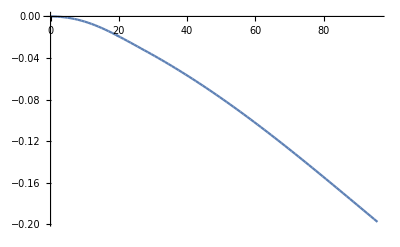

```mathematica
pzL[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);
pzM[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);
pzR[x_]=-(1/2 ρ35k Vcruise^2 S cd)/Lw-py[x]^2/((1/2 ρ35k Vcruise^2 S π *e*AR)/Lw);

nsENGd=20;

Do[
Iyyi[i]=1/12 widthL[(i-1)Leng/nsENGd]^3*heightL[(i-1)Leng/nsENGd]-1/12*(heightL[(i-1)Leng/nsENGd]-2tL[(i-1)Leng/nsENGd])*(widthL[(i-1)Leng/nsENGd]-2tL[(i-1)Leng/nsENGd])^3+4*ASL*(zcL[(i-1)Leng/nsENGd])^2+1/12*(heightL[(i-1)Leng/nsENGd]-2*tL[(i-1)Leng/nsENGd])*tL[(i-1)Leng/nsENGd]^3;
,{i,1,nsENGd}];

Do[
pzi[i][x_]=pzL[x];
Vzi[i][x_]=Integrate[-pzi[i][x],x]+cid[4i-3];
Myi[i][x_]=Integrate[Vzi[i][x],x]+cid[4i-2];
rotzi[i][x_]=Integrate[(-Myi[i][x])/(EE*Iyyi[i]),x]+cid[4i-1];
defzi[i][x_]=Integrate[rotzi[i][x],x]+cid[4i];
,{i,1,nsENGd}];
eqid[1]=rotzi[1][0]==0;
eqid[2]=defzi[1][0]==0;
eqid[3]=Vzi[nsENGd][Leng]+T==Vzi[nsENGd+1][Leng];
eqid[4]=Myi[nsENGd][Leng]==Myi[nsENGd+1][Leng];

nmc=19;
Do[
eqid[4j+1]=Vzi[j][j*Leng/nsENGd]==Vzi[j+1][j*Leng/nsENGd];
eqid[4j+2]=Myi[j][j*Leng/nsENGd]==Myi[j+1][j*Llg/nsENGd];
eqid[4j+3]=rotzi[j][j*Leng/nsENGd]==rotzi[j+1][j*Leng/nsENGd];
eqid[4j+4]=defzi[j][j*Leng/nsENGd]==defzi[j+1][j*Leng/nsENGd];
,{j,1,nmc}];

nsTPd=8;
Do[
Iyyi[i]=1/12 widthL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]^3*heightL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]-1/12*(heightL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]-2tL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd])*(widthL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]-2tL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd])^3+4*ASL*(zcL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd])^2+1/12*(heightL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]-2*tL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd])*tL[Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd]^3;
,{i,1+nsENGd,nsENGd+nsTPd}];
Do[
pzi[i][x_]=pzL[x];
Vzi[i][x_]=Integrate[-pzi[i][x],x]+cid[4i-3];
Myi[i][x_]=Integrate[Vzi[i][x],x]+cid[4i-2];
rotzi[i][x_]=Integrate[(-Myi[i][x])/(EE*Iyyi[i]),x]+cid[4i-1];
defzi[i][x_]=Integrate[rotzi[i][x],x]+cid[4i];
,{i,1+nsENGd,nsENGd+nsTPd}];
eqid[81]=rotzi[nsENGd][Leng]==rotzi[nsENGd+1][Leng];
eqid[82]=defzi[nsENGd][Leng]==defzi[nsENGd+1][Leng];
eqid[83]=Vzi[nsENGd+nsTPd][Ltaper]==Vzi[nsENGd+nsTPd+1][Ltaper];
eqid[84]=Myi[nsENGd+nsTPd][Ltaper]==Myi[nsENGd+nsTPd+1][Ltaper];
nmc=7;
Do[
eqid[4j+1]=Vzi[j][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd]==Vzi[j+1][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd];
eqid[4j+2]=Myi[j][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd]==Myi[j+1][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd];
eqid[4j+3]=rotzi[j][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd]==rotzi[j+1][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd];
eqid[4j+4]=defzi[j][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd]==defzi[j+1][Leng+(j-nsTPd)*(Ltaper-Leng)/nsTPd];
,{j,1+nsENGd,nsENGd+nmc}];

nsLWd=68;
Do[
Iyyi[i]=1/12 widthR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]^3*heightR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]-1/12*(heightR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]-2tR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd])*(widthR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]-2tR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd])^3+4*ASR*(zcR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd])^2+1/12*(heightR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]-2*tR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd])*tR[Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]^3;
,{i,1+nsENGd+nsTPd,nsENGd+nsTPd+nsLWd}];
Do[
pzi[i][x_]=pzL[x];
Vzi[i][x_]=Integrate[-pzi[i][x],x]+cid[4i-3];
Myi[i][x_]=Integrate[Vzi[i][x],x]+cid[4i-2];
rotzi[i][x_]=Integrate[(-Myi[i][x])/(EE*Iyyi[i]),x]+cid[4i-1];
defzi[i][x_]=Integrate[rotzi[i][x],x]+cid[4i];
,{i,1+nsENGd+nsTPd,nsENGd+nsTPd+nsLWd}];
eqid[113]=rotzi[nsENGd+nsTPd][Ltaper]==rotzi[nsENGd+nsTPd+1][Ltaper];
eqid[114]=defzi[nsENGd+nsTPd][Ltaper]==defzi[nsENGd+nsTPd+1][Ltaper];
eqid[115]=Vzi[nsENGd+nsTPd+nsLWd][Lw]==0;
eqid[116]=Myi[nsENGd+nsTPd+nsLWd][Lw]==0;
nmc=67;
Do[
eqid[4j+1]=Vzi[j][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]==Vzi[j+1][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd];
eqid[4j+2]=Myi[j][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]==Myi[j+1][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd];
eqid[4j+3]=rotzi[j][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]==rotzi[j+1][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd];
eqid[4j+4]=defzi[j][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd]==defzi[j+1][Ltaper+(j-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd];
,{j,1+nsENGd+nsTPd,nsENGd+nsTPd+nmc}];

sold=Solve[Table[eqid[n],{n,384}],Table[cid[n],{n,384}]];

Do[
cid[i]=cid[i]/.sold[[1]];
,{i,1,384}];

Do[
pltdefid[i]=Plot[defzi[i][x],{x,(i-1)*Leng/nsENGd,i*Leng/nsENGd}];
,{i,1,nsENGd}];
Do[
pltdefid[i]=Plot[defzi[i][x],{x,Leng+(i-1-nsENGd)*(Ltaper-Leng)/nsTPd,Leng+(i-nsLG)*(Ltaper-Leng)/nsTPd}];
,{i,nsENGd+1,nsENGd+nsTPd}];
Do[
pltdefid[i]=Plot[defzi[i][x],{x,Ltaper+(i-1-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd,Ltaper+(i-nsENGd-nsTPd)*(Lw-Ltaper)/nsLWd}];
,{i,nsLG+nsENG+1,nsENGd+nsTPd+nsLWd}];


Show[Table[pltdefid[n],{n,nsENGd+nsTPd+nsLWd}],PlotRange->{{0,Lw},{0,defzi[96][Lw]}}]
```

### Stress

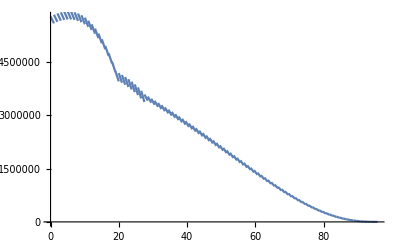

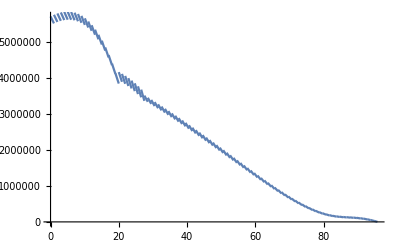

```mathematica
nsLGσ=10;
nsENGσ=10;
nsTPσ=8;
nsLWσ=68;

Do[
σxxi[i][x_]=Abs[(Myi[i][x]*(-widthL[x])/2)/Iyyi[i]]+Abs[(Mzi[i][x]*heightL[x]/2)/Izzi[i]];
,{i,1,28}];
nsENGσ=10;
Do[
σxxi[i][x_]=Abs[(Myi[i][x]*(-widthR[x])/2)/Iyyi[i]]+Abs[(Mzi[i][x]*heightR[x]/2)/Izzi[i]];
,{i,1+28,96}];

Do[
pltσi[i]=Plot[σxxi[i][x],{x,(i-1)*Llg/nsLGσ,i*Llg/nsLGσ}];
,{i,1,nsLGσ}];
Do[
pltσi[i]=Plot[σxxi[i][x],{x,Llg+(i-1-nsLGσ)*(Leng-Llg)/nsENGσ,Llg+(i-nsLGσ)*(Leng-Llg)/nsENGσ}];
,{i,nsLGσ+1,nsLGσ+nsENGσ}];
Do[
pltσi[i]=Plot[σxxi[i][x],{x,Leng+(i-1-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ,Leng+(i-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ}];
,{i,nsLGσ+nsENGσ+1,nsLGσ+nsENGσ+nsTPσ}];
Do[
pltσi[i]=Plot[σxxi[i][x],{x,Ltaper+(i-1-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ,Ltaper+(i-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ}];
,{i,nsLGσ+nsENGσ+nsTPσ+1,nsLGσ+nsENGσ+nsTPσ+nsLWσ}];

(*Von Mises*)
θ=ArcTan[heightL[0]/widthL[0]];
Do[
σyyi[i][x_]=σxθi[i][x]*Sin[θ];
σzzi[i][x_]=σxθi[i][x]*Cos[θ];
,{i,1,96}];

Do[
σxyi[i][x_]=0;
σxzi[i][x_]=0;
,{i,1,96}];

Do[
σMisesi[i][x_]=√(1/2((σxxi[i][x]-σyyi[i][x])^2+(σyyi[i][x]-σzzi[i][x])^2+(σzzi[i][x]-σxxi[i][x])^2+6((σxyi[i][x])^2+(σxzi[i][x])^2)));
,{i,1,96}]

Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,(i-1)*Llg/nsLGσ,i*Llg/nsLGσ}];
,{i,1,nsLGσ}];
Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,Llg+(i-1-nsLGσ)*(Leng-Llg)/nsENGσ,Llg+(i-nsLGσ)*(Leng-Llg)/nsENGσ}];
,{i,nsLGσ+1,nsLGσ+nsENGσ}];
Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,Leng+(i-1-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ,Leng+(i-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ}];
,{i,nsLGσ+nsENGσ+1,nsLGσ+nsENGσ+nsTPσ}];
Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,Ltaper+(i-1-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ,Ltaper+(i-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ}];
,{i,nsLGσ+nsENGσ+nsTPσ+1,nsLGσ+nsENGσ+nsTPσ+nsLWσ}];







Show[Table[pltσi[n],{n,nsLGσ+nsENGσ+nsTPσ+nsLWσ}],PlotRange->{{0,Lw},{0,σxxi[1][0]}},AxesOrigin->{0,0}]

Show[Table[pltσMi[n],{n,nsLGσ+nsENGσ+nsTPσ+nsLWσ}],PlotRange->{{0,Lw},{0,σMisesi[1][0]}},AxesOrigin->{0,0}]
```

### Overall Plots

```mathematica
pl1=Plot[IzzR[x],{x,0,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
pl2=Plot[IzzL[x],{x,0,Lw},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
Show[{pl1,pl2},PlotRange->All,PlotLabel->"Izz",AxesOrigin->{0,0}]

pl3=Plot[VyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl4=Plot[VyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl5=Plot[VyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl6=Plot[VyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl3,pl4,pl5,pl6},PlotRange->All,PlotLabel->"Vy",AxesOrigin->{0,0}]

pl7=Plot[MzL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl8=Plot[MzLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl9=Plot[MzRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl10=Plot[MzR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl7,pl8,pl9,pl10},PlotRange->All,PlotLabel->"Mz",AxesOrigin->{0,0}]

pl11=Plot[rotyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl12=Plot[rotyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl13=Plot[rotyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl14=Plot[rotyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl11,pl12,pl13,pl14},PlotRange->All,PlotLabel->"roty",AxesOrigin->{0,0}]

pl15=Plot[uyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl16=Plot[uyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl17=Plot[uyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl18=Plot[uyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl15,pl16,pl17,pl18},PlotRange->All,PlotLabel->"uy",AxesOrigin->{0,0}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

### Comments

```mathematica
(*Show[%8017,AxesLabel->{HoldForm[Location of Engine ft],HoldForm[Deflection ft]},PlotLabel->HoldForm[Tip Deflection ft vs Location of Engine ft Case 2],LabelStyle->{GrayLevel[0]}]*)
```

```mathematica
Show[%8086,AxesLabel->{HoldForm["Location of Engine (ft)"],HoldForm["Stress (Pa)"]},PlotLabel->HoldForm["Stress at 27.5ft Max vs Engine Location Case 2"],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Plus is not a type of graphics.

Show[0.000153894 (24.98-0.223133 (-27.5+x))^2+5.41889×10^-6 (24.98-0.223133 (-27.5+x))^4,AxesLabel→{Location of Engine (ft),Stress (Pa)},PlotLabel→Stress at 27.5ft Max vs Engine Location Case 2,LabelStyle→{GrayLevel[0]}]

```mathematica
maxLeng=Solve[T*(Leng+Rfuse)== 5390000/FS,Leng];
maxLeng=Leng/.maxLeng[[1]];
```

Solve::ivar: 20 is not a valid variable.

ReplaceAll::reps: {False} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
σxxR[27.5,20]
```

σxxR[27.5,20]

## Constants

```mathematica
ClearAll["Global`*"]
tf=.018675;
gfactor=1;
g=32.174*gfactor;(*gravity (ft/s2)*)
croot=38.94;(*chord at root (ft)*)
ctip=9.735;(*chord at tip (ft)*)
Wto=550000;(*take off weight (lbs)*)
Vcruise=490*1.68781;(*cruise velocity (ft/s)*)
Lw=95.8;(*wing lenght (ft)*)
Weng=10000;(*weight engine (lbs)*)
chordL[x_]=38.94+x*Tan[11.780589303200827 Degree]-x*Tan[35.61 Degree];
chordR[x_]=24.98+(x-27.5)*Tan[26.24608449458938 Degree]-(x-27.5)*Tan[35.61 Degree];

(*chord function of x to end*)
(*chord[x_]=Piecewise[{chordL[x],{0≤x<27.5}},{chordR[x],{27.5≤x≤95.8}}];
width[x_]=.65*chord[x];(*box breadth (ft)*)
height[x_]=0.04666 chord[x];*)(*box height (ft)*)
heightL[x_]=.04666*chordL[x];
widthL[x_]=.65*chordL[x];
heightR[x_]=.04666*chordR[x];
widthR[x_]=.65*chordR[x];

AwebL[x_]=tL[x]*(heightL[x]-2*tL[x]);
AwebR[x_]=tR[x]*(heightR[x]-2*tR[x]);
JL[x_]=1/3 widthL[x] heightL[x]^3; (*torsion constant 0≤x<27.5*)
JR[x_]=1/3 widthR[x] heightR[x]^3;(*torsion constant 27.5≤x<95.8*)
GCF=104427171.365; (*psf*)

Cm=.016;(*moment coefficient at 11 degree AoA*)

(*widthL[x_]=0.65*chord[x];
heightL[x_]=0.04666*chord[x];
widthR[x_]=0.65*chordR[x];
heightR[x_]=0.04666*chordR[x];*)
e=.862;(*Oswald efficiency factor*)
cl=.3925;(*lift coef.at 3 AoA*)
cd=.0948;(*drag coef.at 3 AoA*)
Wlg=4320;(*weight landing gear (lbs)*)
Wfuel=.3*223378; (*fuel weight (lbs)*)
Llg=10.06; (*landing gear location (ft)*)
S=2062.4; (*wing area (ft2)*)
ρ=0.002377; (*air density (slug/ft3)*)
ρ35k=7.38*10^-4; (*air density (slug/ft3)*)
clmax=1.1263; (*max lift coefficient*)
ρAl=3.1; (*density of aluminum (lb/ft3)*)
(*tcl[x_]=.001;
tcr[x_]=.005;*)
(*tL[x_]=tf*heightR[95.8]
tR[x_]=tf*heightR[95.8];*)
r = 0.15; (*radius of stringer ft*)
r2 = 0.15;
ASL=π*r^2;
ASR= Pi*r2^2;

tL[x_]=tf*heightR[x];
tR[x_]=tf*heightR[x];

Wspar=Integrate[ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])+4*ρAl*ASL,{x,0,27.5}]+Integrate[ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])+4*ρAl*ASR,{x,27.5,95.8}];(*weight of spar (lbs)*)

ycL[x_]=heightL[x]/2;
ycR[x_]=heightR[x]/2;
zcL[x_]=widthL[x]/2;
zcR[x_]=widthR[x]/2;
(*IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2;(*moment of inertia of drag (ft4)*)*)

IzzL[x_]=1/12 widthL[x] *heightL[x]^3-1/12*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])^3+4*ASL*(ycL[x])^2+1/12*tL[x]*(heightL[x]-2*tL[x])^3*2+2*AwebL[x]*((widthL[x]-4tL[x])/6+tL[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyL[x_]=1/12 widthL[x]*heightL[x]^3-1/12*(heightL[x]-2tL[x])*(widthL[x]-2tL[x])^3+4*ASL*(zcL[x])^2+1/12*(heightL[x]-2*tL[x])*tL[x]^3;


IzzR[x_]=1/12 widthR[x] *heightR[x]^3-1/12*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])^3+4*ASR*(ycR[x])^2+1/12*tR[x]*(heightR[x]-2*tR[x])^3*2+2*AwebR[x]*((widthR[x]-4tR[x])/6+tR[x]/2)^2;(*moment of inertia of lift(ft4)*)
IyyR[x_]=1/12 widthR[x]*heightR[x]^3-1/12*(heightR[x]-2tR[x])*(widthR[x]-2tR[x])^3+4*ASR*(zcR[x])^2+1/12*(heightR[x]-2*tR[x])*tR[x]^3;(*moment of inertia of drag (ft4)*)

Vstall=√(Wto/(1/2 ρ S clmax)); (*stall velocity (ft/s)*)
Vto=1.2 Vstall; (*takeoff velocity (ft/s)*)
AR=Lw^2/S; (*aspect ratio*)
EE=1461980399.11; (*modulus of elasticity of Al 6061-T6 (psf)*)
T=90000; (*max thrust of engine (lbs)*)
FS=1.15; (*factor of safety*)
yieldstress=40000*12^2/FS;(*yield stress of wing (lb/ft2)*)
Rfuse=10.02; (*radius of fuselage (ft)*)
Ltaper=27.5;
Leng = 20;

Cost = Wspar*10;(*material cost for spar in $ *)
WC = Wspar/Cost;(*Weight/Cost*)
```

ClearAll::wrsym: Symbol σxxLb is Protected.

ClearAll::wrsym: Symbol σxxLc is Protected.

ClearAll::wrsym: Symbol σxxM1b is Protected.

General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.

## Case 3 (Static)

### Lift

```mathematica
a=17.58; b=22.85; c=53.27; d=74.63;
 e=93.18; f=118.32; g=144.42; h=156.11;
sol3a=Solve[0== -Wto*(67)+2*Flg*(e-a),Flg]
Flg=Flg/.sol3a[[1]];
```

{{Flg→243717.}}

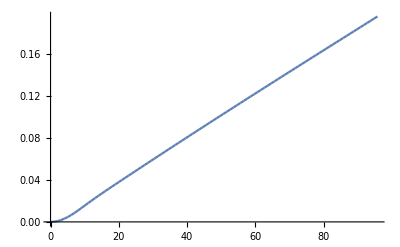

```mathematica
(* distributed load *)
py[x_]=0;
PyWL[x_]=ρAl*widthL[x]*heightL[x]-ρAl*(widthL[x]-2tL[x])*(heightL[x]-2tL[x])+4*ρAl*ASL;
PyWR[x_]=ρAl*widthR[x]*heightR[x]-ρAl*(widthR[x]-2tR[x])*(heightR[x]-2tR[x])+4*ρAl*ASL;

nsLG=10;

Do[
Izzi[i]=1/12 widthL[(i-1)*Llg/nsLG] *heightL[(i-1)*Llg/nsLG]^3-1/12*(widthL[(i-1)*Llg/nsLG]-2tL[(i-1)*Llg/nsLG])*(heightL[(i-1)*Llg/nsLG]-2tL[(i-1)*Llg/nsLG])^3+4*ASL*(ycL[(i-1)*Llg/nsLG])^2+1/12*tL[(i-1)*Llg/nsLG]*(heightL[(i-1)*Llg/nsLG]-2*tL[(i-1)*Llg/nsLG])^3*2+2*AwebL[(i-1)*Llg/nsLG]*((widthL[(i-1)*Llg/nsLG]-4tL[(i-1)*Llg/nsLG])/6+tL[(i-1)*Llg/nsLG]/2)^2;
,{i,1,nsLG}];

Do[
pyi[i][x_]=py[x]-Wfuel/Llg-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,1,nsLG}]

eqi[1]=rotyi[1][0]==0;
eqi[2]=defyi[1][0]==0;
eqi[3]=Vyi[nsLG][Llg]+Wlg-Flg==Vyi[nsLG+1][Llg];
eqi[4]=Mzi[nsLG][Llg]==Mzi[nsLG+1][Llg];
nmc=9;

Do[
eqi[4j+1]=Vyi[j][j*Llg/nsLG]==Vyi[j+1][j*Llg/nsLG];
eqi[4j+2]=Mzi[j][j*Llg/nsLG]==Mzi[j+1][j*Llg/nsLG];
eqi[4j+3]=rotyi[j][j*Llg/nsLG]==rotyi[j+1][j*Llg/nsLG];
eqi[4j+4]=defyi[j][j*Llg/nsLG]==defyi[j+1][j*Llg/nsLG];
,{j,1,nmc}];

nsENG=10;
Do[
Izzi[i]=1/12 widthL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG] *heightL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]^3-1/12*(widthL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-2tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])*(heightL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-2tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])^3+4*ASL*(ycL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])^2+1/12*tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]*(heightL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-2*tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])^3*2+2*AwebL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]*(1/6(widthL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]-4tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG])+tL[Llg+(i-1-nsLG)*(Leng-Llg)/nsENG]/2)^2;
,{i,nsLG+1,nsLG+nsENG}];

Do[
pyi[i][x_]=py[x]-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,1+nsLG,nsLG+nsENG}]

eqi[41]=rotyi[nsLG][Llg]==rotyi[nsLG+1][Llg];
eqi[42]=defyi[nsLG][Llg]==defyi[nsLG+1][Llg];
eqi[43]=Vyi[nsLG+nsENG][Leng]+Weng==Vyi[nsLG+nsENG+1][Leng];
eqi[44]=Mzi[nsLG+nsENG][Leng]==Mzi[nsLG+nsENG+1][Leng];
nmc=9;

Do[
eqi[4j+1]=Vyi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==Vyi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
eqi[4j+2]=Mzi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==Mzi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
eqi[4j+3]=rotyi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==rotyi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
eqi[4j+4]=defyi[j][Llg+(j-nsLG)*(Leng-Llg)/nsENG]==defyi[j+1][Llg+(j-nsLG)*(Leng-Llg)/nsENG];
,{j,nsLG+1,nmc+nsENG}];

nsTP=8;
Do[
Izzi[i]=1/12 widthL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP] *heightL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]^3-1/12*(widthL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-2tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])*(heightL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-2tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])^3+4*ASL*(ycL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])^2+1/12*tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]*(heightL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-2*tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])^3*2+2*AwebL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]*(1/6(widthL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]-4tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP])+tL[Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP]/2)^2;
,{i,nsLG+nsENG+1,nsLG+nsENG+nsTP}];
Do[
pyi[i][x_]=py[x]-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,1+nsLG+nsENG,nsLG+nsENG+nsTP}]

eqi[81]=rotyi[nsLG+nsENG][Leng]==rotyi[nsLG+nsENG+1][Leng];
eqi[82]=defyi[nsLG+nsENG][Leng]==defyi[nsLG+nsENG+1][Leng];
eqi[83]=Vyi[nsLG+nsENG+nsTP][Lw]==Vyi[nsLG+nsENG+nsTP+1][Ltaper];
eqi[84]=Mzi[nsLG+nsENG+nsTP][Ltaper]==Mzi[nsLG+nsENG+nsTP+1][Ltaper];

nmc=7;

Do[
eqi[4j+1]=Vyi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==Vyi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
eqi[4j+2]=Mzi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==Mzi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
eqi[4j+3]=rotyi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==rotyi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
eqi[4j+4]=defyi[j][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP]==defyi[j+1][Leng+(j-nsLG-nsENG)*(Ltaper-Leng)/nsTP];
,{j,nsLG+nsENG+1,nmc+nsENG+nsLG}];

nsWNG=68;
Do[
Izzi[i]=1/12 widthR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG] *heightR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]^3-1/12*(widthR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-2tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])*(heightR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-2tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])^3+4*ASR*(ycR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])^2+1/12*tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]*(heightR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-2*tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])^3*2+2*AwebR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]*(1/6(widthR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]-4tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG])+tR[Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]/2)^2;
,{i,nsLG+nsENG+nsTP+1,nsLG+nsENG+nsTP+nsWNG}];

Do[
pyi[i][x_]=py[x]-PyWL[x];
Vyi[i][x_]=Integrate[-pyi[i][x],x]+ci[4i-3];
Mzi[i][x_]=Integrate[-Vyi[i][x],x]+ci[4i-2];
rotyi[i][x_]=Integrate[(Mzi[i][x])/(EE*Izzi[i]),x]+ci[4i-1];
defyi[i][x_]=Integrate[rotyi[i][x],x]+ci[4i];
,{i,nsLG+nsENG+nsTP+1,nsLG+nsENG+nsTP+nsWNG}];

eqi[113]=rotyi[nsLG+nsENG+nsTP][Ltaper]==rotyi[nsLG+nsENG+nsTP+1][Ltaper];
eqi[114]=defyi[nsLG+nsENG+nsTP][Ltaper]==defyi[nsLG+nsENG+nsTP+1][Ltaper];
eqi[115]=Vyi[nsLG+nsENG+nsTP+nsWNG][Lw]==0;
eqi[116]=Mzi[nsLG+nsENG+nsTP+nsWNG][Lw]==0;

nmc=67;
Do[
eqi[4j+1]=Vyi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==Vyi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
eqi[4j+2]=Mzi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==Mzi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
eqi[4j+3]=rotyi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==rotyi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
eqi[4j+4]=defyi[j][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG]==defyi[j+1][Ltaper+(j-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG];
,{j,nsLG+nsENG+nsTP+1,nmc+nsENG+nsLG+nsTP}];



soll=Solve[Table[eqi[n],{n,384}],Table[ci[n],{n,384}]];

Do[
ci[i]=ci[i]/.soll[[1]];
,{i,1,384}];

Do[
pltdefi[i]=Plot[defyi[i][x],{x,(i-1)*Llg/nsLG,i*Llg/nsLG}];
,{i,1,nsLG}];
Do[
pltdefi[i]=Plot[defyi[i][x],{x,Llg+(i-1-nsLG)*(Leng-Llg)/nsENG,Llg+(i-nsLG)*(Leng-Llg)/nsENG}];
,{i,nsLG+1,nsLG+nsENG}];
Do[
pltdefi[i]=Plot[defyi[i][x],{x,Leng+(i-1-nsLG-nsENG)*(Ltaper-Leng)/nsTP,Leng+(i-nsLG-nsENG)*(Ltaper-Leng)/nsTP}];
,{i,nsLG+nsENG+1,nsLG+nsENG+nsTP}];
Do[
pltdefi[i]=Plot[defyi[i][x],{x,Ltaper+(i-1-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG,Ltaper+(i-nsLG-nsENG-nsTP)*(Lw-Ltaper)/nsWNG}];
,{i,nsLG+nsENG+nsTP+1,nsLG+nsENG+nsTP+nsWNG}];

Show[Table[pltdefi[n],{n,nsLG+nsENG+nsTP+nsWNG}],PlotRange->{{0,Lw},{0,defyi[96][Lw]}}]
```

### Torsion

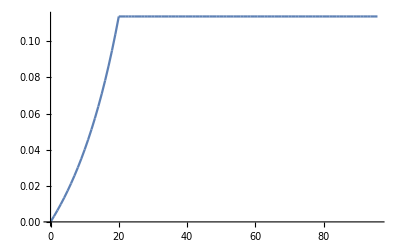

```mathematica
MtL[x]=0;
MtR[x]=0;

(*0<x<Leng*)
nsENGj=20;
Do[
Ji[i]=1/3 widthL[(i)Leng/nsENGj] heightL[(i)Leng/nsENGj]^3;
,{i,1,nsENGj}]; 
Do[
Mti[i][x_]=MtL[x]+cij[2i-1];
ϕti[i][x_]=Integrate[(Mti[i][x])/(GCF*Ji[i]),x]+cij[2i];
,{i,1,nsENGj}];

eqij[1]=ϕti[1][0]==0;
eqij[2]=Mti[nsENGj][Leng]+Leng*18.5-T*3==Mti[nsENGj+1][Leng];
nmc=19;
Do[
eqij[2j+1]=Mti[j][j Leng/nsENGj]==Mti[j+1][j Leng/nsENGj];
eqij[2j+2]=ϕti[j][j Leng/nsENGj]==ϕti[j+1][j Leng/nsENGj];
,{j,1,nmc}];

(*Leng < x < Ltaper*)
nsTPj=8;
Do[
Ji[i]=1/3 widthL[Leng+(i-nsENGj)*(Ltaper-Leng)/nsTPj] heightL[Leng+(i-nsENGj)*(Ltaper-Leng)/nsTPj]^3;
,{i,1+nsENGj,nsENGj+nsTPj}]; 
Do[
Mti[i][x_]=MtL[x]+cij[2i-1];
ϕti[i][x_]=Integrate[(Mti[i][x])/(GCF*Ji[i]),x]+cij[2i];
,{i,1+nsENGj,nsENGj+nsTPj}];
eqij[41]=ϕti[nsENGj][Leng]==ϕti[nsENGj+1][Leng];
eqij[42]=Mti[nsENGj+nsTPj][Ltaper]==ϕti[nsENGj+nsTPj+1][Ltaper];
nmc=7;
Do[
eqij[2j+1]=Mti[j][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj]==Mti[j+1][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj];
eqij[2j+2]=ϕti[j][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj]==ϕti[j+1][Leng+(j-nsENGj)*(Ltaper-Leng)/nsTPj];
,{j,1+nsENGj,nsENGj+nmc}];

(*Ltaper<x<Lw*)
nsLWj=68;
Do[
Ji[i]=1/3 widthR[Ltaper+(i-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj] heightR[Ltaper+(i-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]^3;
,{i,1+nsENGj+nsTPj,nsENGj+nsTPj+nsLWj}]; 
Do[
Mti[i][x_]=MtR[x]+cij[2i-1];
ϕti[i][x_]=Integrate[(Mti[i][x])/(GCF*Ji[i]),x]+cij[2i];
,{i,1+nsENGj+nsTPj,nsENGj+nsTPj+nsLWj}];
eqij[57]=ϕti[nsENGj+nsTPj][Ltaper]==ϕti[nsENGj+nsTPj+1][Ltaper];
eqij[58]=Mti[nsENGj+nsTPj+nsLWj][Lw]==0;
nmc=67;
Do[
eqij[2j+1]=Mti[j][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]==Mti[j+1][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj];
eqij[2j+2]=ϕti[j][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]==ϕti[j+1][Ltaper+(j-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj];
,{j,1+nsENGj+nsTPj,nsENGj+nsTPj+nmc}];
solj=Solve[Table[eqij[n],{n,192}],Table[cij[n],{n,192}]];

Do[
cij[i]=cij[i]/.solj[[1]];
,{i,1,192}];

Do[
plttwist[i]=Plot[ϕti[i][x]*180/π,{x,(i-1)*Leng/nsENGj,i*Leng/nsENGj}];
,{i,1,nsENGj}];
Do[
plttwist[i]=Plot[ϕti[i][x]*180/π,{x,Leng+(i-1-nsENGj)*(Ltaper-Leng)/nsTPj,Leng+(i-nsENGj)*(Ltaper-Leng)/nsTPj}];
,{i,nsENGj+1,nsENGj+nsTPj}];
Do[
plttwist[i]=Plot[ϕti[i][x]*180/π,{x,Ltaper+(i-1-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj,Ltaper+(i-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj}];
,{i,nsENGj+nsTPj+1,nsENGj+nsTPj+nsLWj}];



Do[
maxdi[i]=√((heightL[(i-.5)*Leng/nsENGj]/2)^2+(widthL[(i-.5)*Leng/nsENGj]/2)^2);
,{i,1,nsENGj}];
Do[
maxdi[i]=√((heightL[Leng+(i-.5-nsENGj)*(Ltaper-Leng)/nsTPj]/2)^2+(widthL[Leng+(i-.5-nsENGj)*(Ltaper-Leng)/nsTPj]/2)^2);
,{i,1+nsENGj,nsENGj+nsTPj}];
Do[
maxdi[i]=√((heightR[Ltaper+(i-.5-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]/2)^2+(widthR[Ltaper+(i-.5-nsENGj-nsTPj)*(Lw-Ltaper)/nsLWj]/2)^2);
,{i,1+nsENGj+nsTPj,nsENGj+nsTPj+nsLWj}];

Do[
σxθi[i][x_]=(Mti[i][x]*maxdi[i])/Ji[i];
,{i,1,96}];


Show[Table[plttwist[n],{n,nsENGj+nsTPj+nsLWj}],PlotRange->{{0,Lw},{0,ϕti[96][Lw]*180/π}}]
```

### Stress

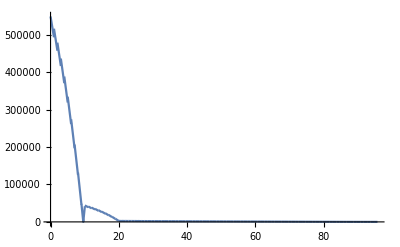

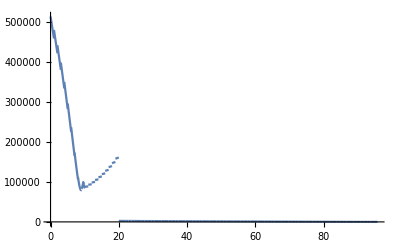

```mathematica
nsLGσ=10;
nsENGσ=10;
nsTPσ=8;
nsLWσ=68;

Do[
σxxi[i][x_]=Abs[(Mzi[i][x]*heightL[x]/2)/Izzi[i]];
,{i,1,28}];
nsENGσ=10;
Do[
σxxi[i][x_]=Abs[(Mzi[i][x]*heightR[x]/2)/Izzi[i]];
,{i,1+28,96}];

Do[
pltσi[i]=Plot[σxxi[i][x],{x,(i-1)*Llg/nsLGσ,i*Llg/nsLGσ}];
,{i,1,nsLGσ}];
Do[
pltσi[i]=Plot[σxxi[i][x],{x,Llg+(i-1-nsLGσ)*(Leng-Llg)/nsENGσ,Llg+(i-nsLGσ)*(Leng-Llg)/nsENGσ}];
,{i,nsLGσ+1,nsLGσ+nsENGσ}];
Do[
pltσi[i]=Plot[σxxi[i][x],{x,Leng+(i-1-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ,Leng+(i-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ}];
,{i,nsLGσ+nsENGσ+1,nsLGσ+nsENGσ+nsTPσ}];
Do[
pltσi[i]=Plot[σxxi[i][x],{x,Ltaper+(i-1-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ,Ltaper+(i-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ}];
,{i,nsLGσ+nsENGσ+nsTPσ+1,nsLGσ+nsENGσ+nsTPσ+nsLWσ}];

(*Von Mises*)
θ=ArcTan[heightL[0]/widthL[0]];
Do[
σyyi[i][x_]=σxθi[i][x]*Sin[θ];
σzzi[i][x_]=σxθi[i][x]*Cos[θ];
,{i,1,96}];

Do[
σxyi[i][x_]=0;
σxzi[i][x_]=0;
,{i,1,96}];

Do[
σMisesi[i][x_]=√(1/2((σxxi[i][x]-σyyi[i][x])^2+(σyyi[i][x]-σzzi[i][x])^2+(σzzi[i][x]-σxxi[i][x])^2+6((σxyi[i][x])^2+(σxzi[i][x])^2)));
,{i,1,96}]

Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,(i-1)*Llg/nsLGσ,i*Llg/nsLGσ}];
,{i,1,nsLGσ}];
Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,Llg+(i-1-nsLGσ)*(Leng-Llg)/nsENGσ,Llg+(i-nsLGσ)*(Leng-Llg)/nsENGσ}];
,{i,nsLGσ+1,nsLGσ+nsENGσ}];
Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,Leng+(i-1-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ,Leng+(i-nsLGσ-nsENGσ)*(Ltaper-Leng)/nsTPσ}];
,{i,nsLGσ+nsENGσ+1,nsLGσ+nsENGσ+nsTPσ}];
Do[
pltσMi[i]=Plot[σMisesi[i][x],{x,Ltaper+(i-1-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ,Ltaper+(i-nsLGσ-nsENGσ-nsTPσ)*(Lw-Ltaper)/nsLWσ}];
,{i,nsLGσ+nsENGσ+nsTPσ+1,nsLGσ+nsENGσ+nsTPσ+nsLWσ}];







Show[Table[pltσi[n],{n,nsLGσ+nsENGσ+nsTPσ+nsLWσ}],PlotRange->{{0,Lw},{0,σxxi[1][0]}},AxesOrigin->{0,0}]

Show[Table[pltσMi[n],{n,nsLGσ+nsENGσ+nsTPσ+nsLWσ}],PlotRange->{{0,Lw},{0,σMisesi[1][0]}},AxesOrigin->{0,0}]
```

### Overall Plots

```mathematica
pl1=Plot[IzzR[x],{x,0,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
pl2=Plot[IzzL[x],{x,0,Lw},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
Show[{pl1,pl2},PlotRange->All,PlotLabel->"Izz",AxesOrigin->{0,0}]

pl3=Plot[VyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl4=Plot[VyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl5=Plot[VyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl6=Plot[VyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl3,pl4,pl5,pl6},PlotRange->All,PlotLabel->"Vy",AxesOrigin->{0,0}]

pl7=Plot[MzL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl8=Plot[MzLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl9=Plot[MzRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl10=Plot[MzR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl7,pl8,pl9,pl10},PlotRange->All,PlotLabel->"Mz",AxesOrigin->{0,0}]

pl11=Plot[rotyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl12=Plot[rotyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl13=Plot[rotyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl14=Plot[rotyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl11,pl12,pl13,pl14},PlotRange->All,PlotLabel->"roty",AxesOrigin->{0,0}]

pl15=Plot[uyL[x],{x,0,Llg},PlotStyle->Black,PlotLegends->{"Left"}];
pl16=Plot[uyLM[x],{x,Llg,Leng},PlotStyle->Orange,PlotLegends->{"Left Middle"}];
pl17=Plot[uyRM[x],{x,Leng,Ltaper},PlotStyle->Blue,PlotLegends->{"Right Middle"}];
pl18=Plot[uyR[x],{x,Ltaper,Lw},PlotStyle->Red,PlotLegends->{"Right"}];
Show[{pl15,pl16,pl17,pl18},PlotRange->All,PlotLabel->"uy",AxesOrigin->{0,0}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

### Comments

```mathematica
(*Show[%8776,AxesLabel->{HoldForm["Location of Engine (ft)"],HoldForm["Stress (Pa)"]},PlotLabel->HoldForm["Stress @ 27.5ft along Spar (max) vs Engine Location Case 3"],LabelStyle->{GrayLevel[0]}]*)
```

```mathematica
(*Show[%8772,AxesLabel->{HoldForm[Location of Engine ft],HoldForm[Tip Deflection ft]},PlotLabel->HoldForm[Tip Deflection vs Location of Engine Case 3],LabelStyle->{GrayLevel[0]}]*)
```

```mathematica
(*{{0.13248300656249998,-23.08462321638492},{0.06624150328124999,-11.603174462498314},{0.021197281049999996,11.884766836036333},{0.010598640524999998,41.998900299869774},{0.005299320262499999,101.14113311866477}}*)
```

```mathematica
(*num=(27.5-20)/10;*)
(*uvec={};Do[AppendTo[uvec,uyR[Leng ]],{Leng,20,27.5,num}]
data1=Transpose@{Range[20,27.5,num],uvec};
ListPlot[data1] (*deflection at Leng*);*)


(*uvec2={};Do[AppendTo[uvec2,uyR[Lw]],{Leng,20,27.5,num}];
data2=Transpose@{Range[20,27.5,num],uvec2};
ListPlot[data2] (*deflection at Lw*)*)

(*thick={height/4,height/8,height/12,height/15,height/20,height/25,height/50,height/100};
data1=Transpose@{thick,tipdeflection[Lw,20,thick]}
data2=Transpose@{thick,tipdeflection[Lw,(52.3+20)/2,thick]};
data3=Transpose@{thick,tipdeflection[Lw,52.3,thick]};
ListPlot[{data1,data2,data3},PlotLegends->{"Leftmost Engine","Central Engine","Rightmost Engine"},PlotLabel->"Tip Deflection",AxesLabel->{"Thickness (ft)","Deflection (ft)"}]*)
```

```mathematica
(*num=(27.5-20)/10;*)
(*uvec3={};Do[AppendTo[uvec3,Abs[σxxM2[27.5,Leng]]],{Leng,20,27.5,num}]
data=Transpose@{Range[20,27.5,num],uvec3};
ListPlot[data]*)
```

## Graph

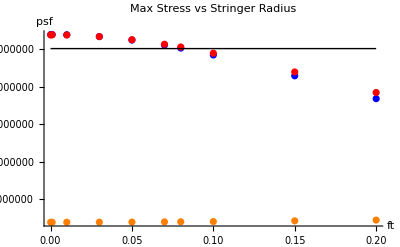

```mathematica
plot1=ListPlot[{{.0001,5.38209*10^6},{.1,4.83883*10^6},{.05,5.23625*10^6},{.2,3.67784*10^6},{.001,5.38203*10^6},{.01,5.37612*10^6},{.08,5.02254*10^6},{.07,5.10284*10^6},{.15,4.28541*10^6},{.03,5.32875*10^6}},PlotStyle->Blue];
plot2=ListPlot[{{.0001,5.37006*10^6},{.1,4.88631*10^6},{.05,5.24414*10^6},{.2,3.84093*10^6},{.001,5.37539*10^6},{.01,5.37006*10^6},{.08,5.05172*10^6},{.07,5.12402*10^6},{.15,4.38802*10^6},{.03,5.32742*10^6}},PlotStyle->Red];
plot3=ListPlot[{{.0001,391576},{.1,409992},{.05,396519},{.2,449373},{.001,391578},{.01,391778},{.08,403764},{.07,401042},{.15,428759},{.03,393384}},PlotStyle->Orange];
l1=Graphics@Line[{{0,5.0087*10^6},{.2,5.0087*10^6}}];
Show[{plot1,plot2,plot3,l1},PlotRange->All,PlotLabel->"Max Stress vs Stringer Radius",AxesLabel->{"ft","psf"},AxesOrigin->{0,0}]
```

```mathematica
Unprotect[plot1a];
Unprotect[plot1b];
Unprotect[plot1c];
Unprotect[plot2a];
Unprotect[plot2b];
Unprotect[plot2c];
Unprotect[plot3a];
Unprotect[plot3b];
Unprotect[plot3c];
Show[{plot1a,plot2a,plot3a,plot1b,plot2b,plot3b,plot1c,plot2c,plot3c},PlotRange->All,PlotLabel->"Angle of Twist along Spar",AxesLabel->{"ft","Degrees"}]
```

Show::gcomb: Could not combine the graphics objects in Show[{plot1a,plot2a,plot3a,plot1b,plot2b,plot3b,plot1c,plot2c,plot3c},PlotRange→All,PlotLabel→Angle of Twist along Spar,AxesLabel→{ft,Degrees}].

Show[{plot1a,plot2a,plot3a,plot1b,plot2b,plot3b,plot1c,plot2c,plot3c},PlotRange→All,PlotLabel→Angle of Twist along Spar,AxesLabel→{ft,Degrees}]

```mathematica
tf=.018675;tf=.018675;
```